```mathematica
plotVectors[A_]:=Module[{u,v1,s,v},
{u, s, v} = SingularValueDecomposition[A];
v1 = v[[All,1]];
Graphics[
{
Circle[{0,0}],
Arrow[{{0,0},u[[All,1]]}],Arrow[{{0,0},u[[All,2]]}]
}
]
Graphics[
{
GeometricTransformation[Circle[{0,0},{s[[1,1]],s[[2,2]]}],RotationTransform[ArcTan[v1[[2]]/v1[[1]]],{0,0}]],
Arrow[{{0,0},s[[1,1]]*v[[All,1]]}],
Arrow[{{0,0},s[[2,2]]*v[[All,2]]}]
}
]
]
```

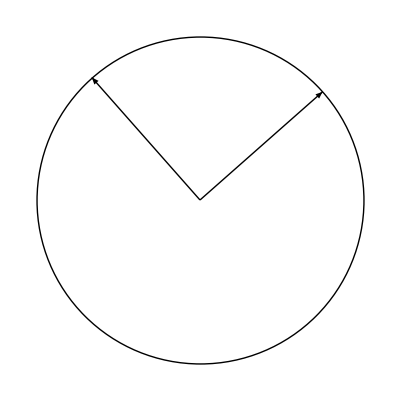
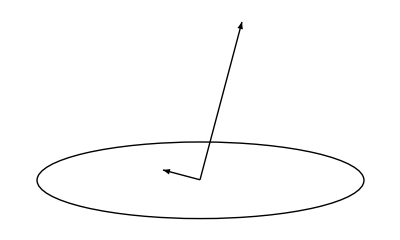

```mathematica
plotVectors[{{1,2},{0,2}}]
```

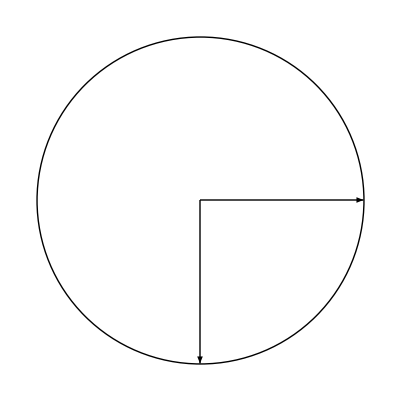
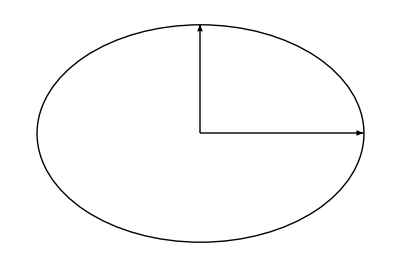

```mathematica
plotVectors[{{3,0},{0,-2}}]
```

```mathematica
plotVectors[{{2,0},{0,3}}]
```

Power::infy: Infinite expression 1/0 encountered.

GeometricTransformation::nonaffine: TransformationFunction[{{Indeterminate,Indeterminate,Indeterminate},{«1»},{Indeterminate,«13»,Indeterminate}}] is not an affine transformation function.

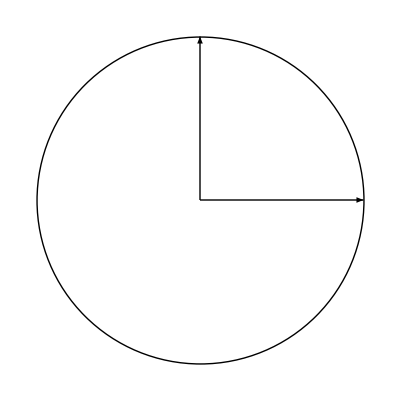
-Graphics- -Graphics-

This one doesn' t work because ArcTan won' t work for it

```mathematica
plotVectors[{{1,1},{0,0}}]
```

-Graphics- -Graphics-

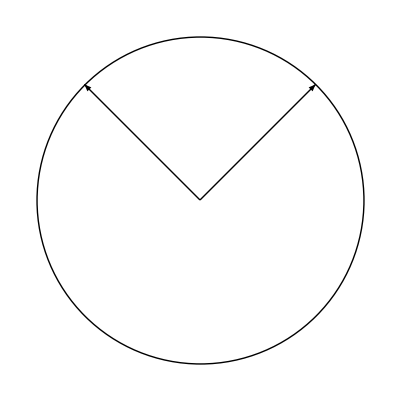
-Graphics- -Graphics-

```mathematica
plotVectors[{{1,1},{1,1}}]
```